Mohamed M. Hammad

Neural Network and Deep Learning with Mathematica                                < >    Ξ

Edited by Hao Feng

## 3 Matrix Calculus and Gradient Optimization

Remark: This chapter provides a Mathematica implementation of the concepts and ideas presented in Chapter 2, [1], of the book titled Artificial Neural Network and Deep Learning: Fundamentals and Theory. We strongly recommend that you begin with the theoretical chapter to build a solid foundation before exploring the corresponding practical implementation. This chapter also serves as a summary of the book titled Mathematics for Machine Learning and Data Science: Optimization with Mathematica Applications. For detailed proofs of theorems, additional examples, and comprehensive explanations, including Mathematica applications, please refer to Ref [11].”

In the realm of AI and machine learning, the modern development of NNs stands as a testament to the marriage of sophisticated mathematical frameworks and computational ingenuity. At the heart of this evolution lies the profound influence of matrix calculus [12-14] and gradient optimization techniques [15-23]. These foundational pillars have not only reshaped the landscape of NN design but have also propelled advancements in diverse domains, ranging from computer vision to natural language processing and beyond.

Matrix calculus, with its roots in linear algebra, provides a powerful toolset for analyzing and manipulating multidimensional data structures. It offers a systematic framework for computing derivatives and gradients of functions involving matrices and vectors, enabling efficient optimization in high-dimensional spaces. Matrix calculus is indeed essential for building and training NNs. NNs, especially deep learning models, heavily rely on matrix operations for their computations.

Here’s why matrix calculus is crucial for NNs:

• NNs are typically represented and implemented using matrices and vectors. Each layer in a NN can be seen as a matrix operation, where inputs (vectors) are multiplied by weights (matrices) and passed through functions (activation functions).

• The training of NNs often involves optimization algorithms like Gradient Descent (GD). Matrix calculus provides the necessary tools to compute gradients efficiently, enabling the optimization process to update the network parameters (weights) in the direction that minimizes the objective (loss) function.

• Backpropagation is the primary algorithm used to compute gradients efficiently in NNs. It is essentially an application of the chain rule from calculus, which involves matrix multiplication and transposition operations.

• Matrix calculus allows for efficient computation of derivatives and gradients in NNs. This efficiency is crucial for training deep NNs, which may have millions of parameters.

• Most deep learning frameworks handle much of the matrix calculus under the hood. However, understanding the underlying principles of matrix calculus can help in debugging, optimizing, and customizing NN architectures.

Complementing matrix calculus is the arsenal of gradient optimization techniques, which are fundamental to training NNs. By iteratively adjusting model parameters in the direction of steepest descent, these methods seek to minimize a predefined objective function, such as the loss function in supervised learning tasks. From classic algorithms like GD to more advanced variants like Stochastic Gradient Descent (SGD) and Adaptive Moment (Adam) optimization, these techniques play a pivotal role in navigating the vast landscape of model parameter space efficiently and effectively.

This chapter aims to introduce the concepts of numerical differentiation, matrix calculus, gradient optimization, and demonstrate their implementation using Mathematica.

• Numerical differentiation is a crucial technique in computational mathematics, enabling the approximation of derivatives from discrete data points. This is particularly useful when analytical differentiation is challenging or impossible.

• Matrix calculus extends traditional calculus to higher dimensions, dealing with functions that map matrices to scalars, vectors, or other matrices.

• Optimization is at the heart of machine learning, where we aim to minimize a loss (or objective) function. Gradient-based methods, such as gradient descent, iteratively adjust the parameters to reduce the loss.

By the end of this chapter, you will be able to:

• Implement matrix calculus operations in Mathematica.

• Implement numerical differentiation techniques in Mathematica.

• Utilize Mathematica to perform gradient-based optimization.

This chapter will include detailed explanations, examples, and Mathematica code snippets to ensure a comprehensive understanding of these topics.

code 3.1

(* The code demonstrates the numerical approximation of the first derivative of
the function f(x)= sin(x) at x0=Pi/4 using finite difference methods. It calculates
the forward, backward, and central difference approximations with a step size
h=0.1,and compares these results to the exact derivative obtained analytically.
The code prints the approximations and the exact derivative, and generates a plot
of the function over the interval [x_0-h,x_0+h], highlighting the point at x0
where the derivative is approximated: *)

Forward Difference Approximation: 0.670603

Backward Difference Approximation: 0.741255

Central Difference Approximation: 0.705929

Exact Derivative: 0.707107

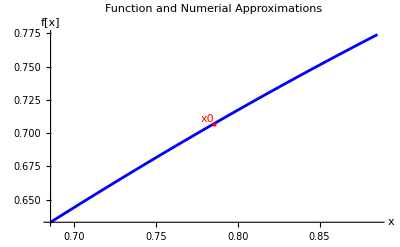

```mathematica
f[x_]:=Sin[x]
x0=π/4;
h=0.1;

forwardDifference=(f[x0+h]-f[x0])/h;
backwardDifference=(f[x0]-f[x0-h])/h;
centralDifference=(f[x0+h]-f[x0-h])/(2h);

exactDerivate=D[f[x],x]/.x->x0;

Print["Forward Difference Approximation: ",forwardDifference]
Print["Backward Difference Approximation: ",backwardDifference]
Print["Central Difference Approximation: ",centralDifference]
Print["Exact Derivative: ",N[exactDerivate]]

plotFunction=Plot[
f[x],
{x,x0-h,x0+h},
PlotStyle->Blue,
PlotLabel->"Function and Numerial Approximations",
Epilog->{
Red,
PointSize[Large],
Point[{x0,f[x0]}],
Text["x0",{x0,f[x0]},{1,-1}]
},
AxesLabel->{"x","f[x]"}
];

Show[plotFunction]
```

code 3.2

(* The goal of the `Manipulate` code is to dynamically illustrate and compare the
numerical approximations of the first derivative of the function f(x)= sin(x) at
x0=Pi/4 using finite difference methods (forward, backward, and central
differences) with a variable step size h. The code calculates these approximations
and the exact derivative, displays the results, and plots the function along with
the tangent lines corresponding to the numerical approximations. The interactive
slider allows users to adjust the step size h, providing a visual and numerical
understanding of how the step size affects the accuracy of the derivative
approximations: *)

```mathematica
Manipulate[
Module[
{f,x0,forwardDifference,backwardDifference,centralDifference,exactDerivate,plotFunction},
f[x_]:=Sin[x];
x0=π/4;

forwardDifference=(f[x0+h]-f[x0])/h;
backwardDifference=(f[x0]-f[x0-h])/h;
centralDifference=(f[x0+h]-f[x0-h])/(2h);
exactDerivate=D[f[x],x]/.x->x0;

Column[
{
Row[{"Step size (h): ",NumberForm[h,{4,2}]}],
Row[{"Forward Difference Approximation: ",NumberForm[forwardDifference,{8,6}]}],
Row[{"Backward Difference Approximation: ",NumberForm[backwardDifference,{8,6}]}],
Row[{"Central Difference Approximation: ",NumberForm[centralDifference,{8,6}]}],
Row[{"Exact Derivate: ",NumberForm[exactDerivate,{8,6}]}],
Plot[
{
f[x],
f[x0]+(x-x0)forwardDifference,
f[x0]+(x-x0)backwardDifference,
f[x0]+(x-x0)centralDifference},
{x,x0-2h,x0+2h},
PlotStyle->{Blue,Red,Green,Purple},
PlotLegends->{"f[x]","Forward Approximation","Backward Approximation","Central Approximation"},
Epilog->{
Red,
PointSize[Large],
Point[{x0,f[x0]}],
Text["x0",{x0,f[x0]},{1,-1}]
},
PlotLabel->"Function and Numerical Approximations",
AxesLabel->{"x","f[x]"},
ImageSize->300
]
}
]
],
{{h,0.1,"Step size (h)"},0.001,2,0.01}
]
```

### optimization